# 3 jet fraction in the cross section for e^+e^-→ hadrons

Demonstration how to get this cross section from the lagrangian via different jet algorithms

## Notation and rules

We use vec for vectors, g for the metric tensor and distinguish upper and lower indices:

```mathematica
Format[g[a_,b_],TraditionalForm]:=Subscript[g,SequenceForm[a,b]]
Format[g[up[a_],b_],TraditionalForm]:=Subsuperscript[g,b,a]
Format[g[b_,up[a_]],TraditionalForm]:=Subsuperscript[g,b,a]
Format[g[up[a_],up[b_]],TraditionalForm]:=Superscript[g,SequenceForm[a,b]]
Attributes[g]=Orderless;

Format[γ[a_],TraditionalForm]:=Subscript[γ, a]
Format[γ[up[a_]],TraditionalForm]:=γ^a

Format[vec[a_,b_],TraditionalForm]:=Subscript[a, b]
Format[vec[a_,up[b_]],TraditionalForm]:=a^b
vec[0,_]=0;
```

We use SP for scalar product:

```mathematica
SP[0]=0;
Attributes[SP]=Orderless;
SP[aa_,aa_]:=SP[aa]
SP[aa_,-bb_]:=-SP[aa,bb]
SP[-aa_]:=SP[aa]
Format[SP[a_,b_],TraditionalForm]:=SequenceForm[a,b]
Format[SP[a_],TraditionalForm]:=a^2
SP[0,_]=0;
```

convolution rules

```mathematica
gammasim={a___·γ[up[c_]]·γ[up[d_]]·b___ vec[e_,c_]vec[e_,d_]->(-SP[e])a·b,g[a_,b_]vec[c_,up[b_]]->vec[c,a],g[a_,up[b_]]vec[c_,b_]->vec[c,a],g[a_,up[b_]]g[c_,b_]->g[c,a],g[dd_,up[b_]]c___·γ[b_]·a___->c·γ[dd]·a,g[dd_,b_]c___·γ[up[b_]]·a___->c·γ[dd]·a,vec[ka_,b_]vec[c_,up[b_]]->-SP[ka,c],g[ao_,up[ao_]]->4}
```

{e__c_ e__d_ a___·γ^c_·γ^d_·b___→e^2 (-(a·b)),c_^b_ g_a_b_→c_a,c__b_ g_a_^b_→c_a,g_b_c_ g_a_^b_→g_ac,g_dd_^b_ c___·γ_b_·a___→c·γ_dd·a,g_b_dd_ c___·γ^b_·a___→c·γ_dd·a,c_^b_ ka__b_→-(cka),g_ao_^ao_→4}

## γ-matrix trace (spur) calculation

We use the anticommutator relation for γ-matrices γ^a γ^b+γ^b γ^a=2 g^ab to express the trace of n γ-matrices through traces of n-2 γ-matrices:

Sp takes as argument the Lorenz indices of the γ-matrices and returns the trace

```mathematica
Sp[a__]:=0/;OddQ[Length@{a}];
Module[{a,b,c,d,e,f}, Sp[a__]:=( b=f@@Range[Length[{a}]]; b//.f[c___,1,d_,e___]-> g[1,d]f[c,e]-f[c,d,1,e]/.f[___,1]->0/.Thread[List@@b-> {a}]/.f->Sp); ]
Sp[a_,bf_]:=4g[a,bf];
```

Example tr[γ_a γ_b γ_c γ_d]:

```mathematica
Sp[a,b,c,d]
```

4 g[a,d] g[b,c]-4 g[a,c] g[b,d]+4 g[a,b] g[c,d]

## Cross section for q OverLine(q)-bar gluon production

We have to calculate the sum of 2 diagrams

-Graphics-

The leptonic tensor cancels in the ratio of the 3 jet cross section and the LO 2 jet one. So we do not need it.

The hadronic tensor reads

```mathematica
ht=g[α,β]γ[up[κ11]]·(-(γ[up[α]]·(γ[up[κ2]]vec[k2,κ2]+vec[k3,κ3]γ[up[κ3]])·γ[up[μ]])/SP[k2+k3]+(γ[up[μ]]·(γ[up[κ1]]vec[k1,κ1]+vec[k3,κ3]γ[up[κ3]])·γ[up[α]])/SP[k1+k3])·γ[up[κ22]]·(-(γ[μ]·(γ[up[κ222]]vec[k2,κ222]+vec[k3,κ33]γ[up[κ33]])·γ[up[β]])/SP[k2+k3]+(γ[up[β]]·(γ[up[κ111]]vec[k1,κ111]+vec[k3,κ33]γ[up[κ33]])·γ[μ])/SP[k1+k3])vec[k1,κ11]vec[k2,κ22]
```

γ[up[κ11]]·((γ[up[μ]]·(vec[k1,κ1] γ[up[κ1]]+vec[k3,κ3] γ[up[κ3]])·γ[up[α]])/SP[k1+k3]-(γ[up[α]]·(vec[k2,κ2] γ[up[κ2]]+vec[k3,κ3] γ[up[κ3]])·γ[up[μ]])/SP[k2+k3])·γ[up[κ22]]·((γ[up[β]]·(vec[k1,κ111] γ[up[κ111]]+vec[k3,κ33] γ[up[κ33]])·γ[μ])/SP[k1+k3]-(γ[μ]·(vec[k2,κ222] γ[up[κ222]]+vec[k3,κ33] γ[up[κ33]])·γ[up[β]])/SP[k2+k3]) g[α,β] vec[k1,κ11] vec[k2,κ22]

We expand this expression into a linear combination of γ-matrix products

```mathematica
Attributes[CenterDot]:=Flat;
ht1=ht/.γ[a_]->CenterDot[γ[a]]//.a___·(b_ CenterDot[c_]+d_ CenterDot[e_])·f___->b(a·c·f)+d (a·e·f)
```

k1_κ11 k2_κ22 g_αβ (1/(k1+k3)^2(k3_κ3 ((k1_κ111 γ^κ11·γ^μ·γ^κ3·γ^α·γ^κ22·γ^β·γ^κ111·γ_μ+k3_κ33 γ^κ11·γ^μ·γ^κ3·γ^α·γ^κ22·γ^β·γ^κ33·γ_μ)/(k1+k3)^2-(k2_κ222 γ^κ11·γ^μ·γ^κ3·γ^α·γ^κ22·γ_μ·γ^κ222·γ^β+k3_κ33 γ^κ11·γ^μ·γ^κ3·γ^α·γ^κ22·γ_μ·γ^κ33·γ^β)/(k2+k3)^2)+k1_κ1 ((k1_κ111 γ^κ11·γ^μ·γ^κ1·γ^α·γ^κ22·γ^β·γ^κ111·γ_μ+k3_κ33 γ^κ11·γ^μ·γ^κ1·γ^α·γ^κ22·γ^β·γ^κ33·γ_μ)/(k1+k3)^2-(k2_κ222 γ^κ11·γ^μ·γ^κ1·γ^α·γ^κ22·γ_μ·γ^κ222·γ^β+k3_κ33 γ^κ11·γ^μ·γ^κ1·γ^α·γ^κ22·γ_μ·γ^κ33·γ^β)/(k2+k3)^2))-1/(k2+k3)^2(k3_κ3 ((k1_κ111 γ^κ11·γ^α·γ^κ3·γ^μ·γ^κ22·γ^β·γ^κ111·γ_μ+k3_κ33 γ^κ11·γ^α·γ^κ3·γ^μ·γ^κ22·γ^β·γ^κ33·γ_μ)/(k1+k3)^2-(k2_κ222 γ^κ11·γ^α·γ^κ3·γ^μ·γ^κ22·γ_μ·γ^κ222·γ^β+k3_κ33 γ^κ11·γ^α·γ^κ3·γ^μ·γ^κ22·γ_μ·γ^κ33·γ^β)/(k2+k3)^2)+k2_κ2 ((k1_κ111 γ^κ11·γ^α·γ^κ2·γ^μ·γ^κ22·γ^β·γ^κ111·γ_μ+k3_κ33 γ^κ11·γ^α·γ^κ2·γ^μ·γ^κ22·γ^β·γ^κ33·γ_μ)/(k1+k3)^2-(k2_κ222 γ^κ11·γ^α·γ^κ2·γ^μ·γ^κ22·γ_μ·γ^κ222·γ^β+k3_κ33 γ^κ11·γ^α·γ^κ2·γ^μ·γ^κ22·γ_μ·γ^κ33·γ^β)/(k2+k3)^2)))

and calculate the traces

```mathematica
ht2=Expand[ht1/.cd__CenterDot:>Sp@@cd⟦All,1⟧]//.gammasim
```

(16 k1^2 (k1k2))/(((k1+k3)^2)^2)+(32 k1^2 (k2k3))/(((k1+k3)^2)^2)+(16 k2^2 (k1k2))/(((k2+k3)^2)^2)+(32 k2^2 (k1k3))/(((k2+k3)^2)^2)-(16 k3^2 (k1k2))/(((k1+k3)^2)^2)+(64 k3^2 (k1k2))/((k1+k3)^2 (k2+k3)^2)-(16 k3^2 (k1k2))/(((k2+k3)^2)^2)+(64 (k1k2)^2)/((k1+k3)^2 (k2+k3)^2)+(64 (k1k2) (k1k3))/((k1+k3)^2 (k2+k3)^2)+(64 (k1k2) (k2k3))/((k1+k3)^2 (k2+k3)^2)+(32 (k1k3) (k2k3))/(((k1+k3)^2)^2)+(32 (k1k3) (k2k3))/(((k2+k3)^2)^2)

take into account that the final particles are massless

```mathematica
ht3=ht2/.SP[a_+b_]->SP[a]+SP[b]+2SP[a,b]/.SP[k1]->0/.SP[k2]->0/.SP[k3]->0
```

(16 (k1k2)^2)/((k1k3) (k2k3))+(16 (k1k2))/k1k3+(16 (k1k2))/k2k3+(8 (k2k3))/k1k3+(8 (k1k3))/k2k3

introduce the energy fractions x_i=(2 E_i)/(√s)

```mathematica
ht4=ht3/.SP[k1,k2]-> s(1-x3)/2/.SP[k1,k3]-> s(1-x2)/2/.SP[k3,k2]-> s(1-x1)/2/.x3->2-x1-x2//Factor
```

(8 (x1^2+x2^2))/((-1+x1) (-1+x2))

and write the 3-jet fraction of the differential cross section 1/σ_0dσ/dx1dx2 assuming that αs=0.3

```mathematica
dσ=2/3 αs/(8π) ht4/.αs->0.3
```

(0.063662 (x1^2+x2^2))/((-1+x1) (-1+x2))

## Cross section for 3 jet production

We define the phase space

```mathematica
phaseSpace={x1>0,x2>0,x1+x2>1};
dσ1=dσ Boole[And@@phaseSpace]
```

(0.063662 (x1^2+x2^2) Boole[x1>0&&x2>0&&x1+x2>1])/((-1+x1) (-1+x2))

And draw the differential cross section

```mathematica
Plot3D[dσ1,{x1,0,1},{x2,0,1},PlotPoints->50]
```

-Graphics3D-

Introduce the Durham algorithm cutoff for the 3 jet phase space 2 Min[E_j^2,E_i^2](1-cosθ_ij)>sd

```mathematica
area3jetDurham=And@@{2Min[x1^2,x2^2](x1+x2-1)/(x1 x2)>d,2Min[x1^2,x2^2](x1+x2-1)/(x1 x2)>d/.x2->2-x1-x2,2Min[x1^2,x2^2](x1+x2-1)/(x1 x2)>d/.x1->2-x1-x2}
area[x_]:=Show[DensityPlot[dσ1,{x1,0,1},{x2,0,1},ColorFunctionScaling->False, ColorFunction->((1-Tanh[.1#])&),PlotRange->All],RegionPlot[area3jetDurham/.d->x,{x1,0,1},{x2,0,1},PlotPoints->10,GridLines->Automatic],AxesLabel->{"x_1","x_2"}]
```

(2 (-1+x1+x2) Min[x1^2,x2^2])/(x1 x2)>d&&(2 (1-x2) Min[x1^2,(2-x1-x2)^2])/(x1 (2-x1-x2))>d&&(2 (1-x1) Min[(2-x1-x2)^2,x2^2])/((2-x1-x2) x2)>d

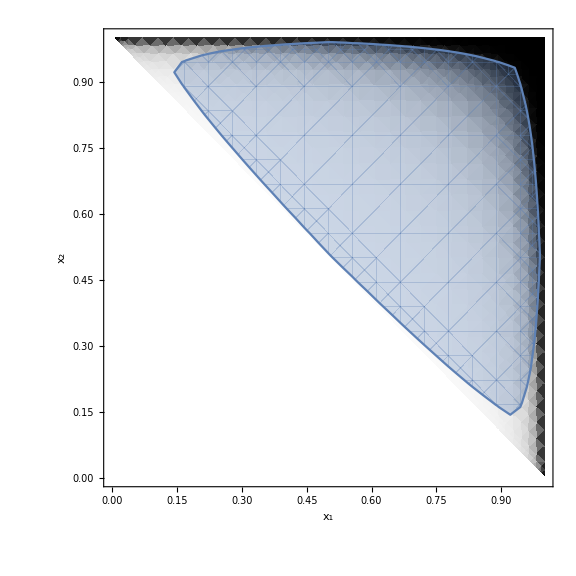

```mathematica
area[.02]
```

Calculate the cross section as function of the jet algorithm parameter d

```mathematica
σDurham[d1_]:=NIntegrate[dσ1 Boole[area3jetDurham]/.d->d1,{x1,0,1},{x2,0,1},Method->"AdaptiveMonteCarlo"]
```

```mathematica
σDurham[0.05]
```

0.418223

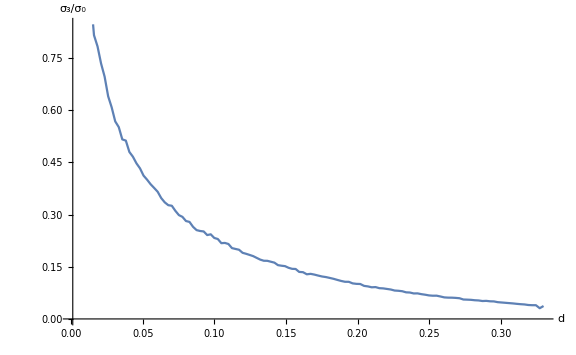

```mathematica
σDurhamPlot=Plot[σDurham[x],{x,0.001,0.33},PlotPoints->3,AxesLabel->{"d","σ_3/σ_0"}]
```

Show all in one interactive output

```mathematica
Manipulate[TableForm[{{SequenceForm["σ_3/σ_0 = ",#],GraphicsRow[{Show[σDurhamPlot,Graphics[{PointSize[Large],Point[{d,#}]}]],area[d]},ImageSize->Large]}}ᵀ]&[σDurham[d]],{{d ,0.1,"Jet parameter d"},0.01,0.33}]
```

## Questions

#### Derive the constant in front of the hadronic tensor 2/3 αs/(8π) Explain what values of the jet algorithm parameter d are physical Do a similar calculation both analytically and symbolically for Jade algorithm: (p_i+p_j)^2<sd

Authorship information

Andrey Grabovsky

Date of creation 20.06.2017

Author email address a.v.grabovsky@inp.nsk.su